## xSSA Example: SSAtoXLR8R

LGPL License applies

This example uses the Repressilator Equations (Elowitz & Liebler, 2000, Nature 403:335-338)

```mathematica
<<xSSA.m;
<<xlr8r.m;
```

xSSA 1.1.α.4 (11-Jul-2009) loaded Sat-11-Jul-2009-15:03:17 using Mathematica 7.0 for Linux x86 (64-bit) (February 18, 2009)(7.0.1)

```mathematica
r={{PZ↦X,sHill[-n,Km,(α ϵ)/τ]},{PX↦Y,sHill[-n,Km,(α ϵ)/τ]},{PY↦Z,sHill[-n,Km,(α ϵ)/τ]},{X->∅,1/τ},{Y->∅,1/τ},{Z->∅,1/τ},{∅->X,(α0 ϵ)/τ},{∅->Y,(α0 ϵ)/τ},{∅->Z,(α0 ϵ)/τ},{X->PX+X,(Km β)/(ϵ τ)},{PX->∅,β/τ},{Y->PY+Y,(Km β)/(ϵ τ)},{PY->∅,β/τ},{Z->PZ+Z,(Km β)/(ϵ τ)},{PZ->∅,β/τ}};
parameters={α->250,α0->250/1000,α1->0,β->.2,n->2,k1-> 1,Km-> 40, τ-> 2/Log[2.], ϵ-> 20};
iv={PX-> 5, PY-> 0, X-> 15};
```

```mathematica
ssim=SSA[r, 20, iv, parameters];
```

Warning: the following variables are missing initial condtions, which are all assumed to be zero: {PZ,Y,Z}

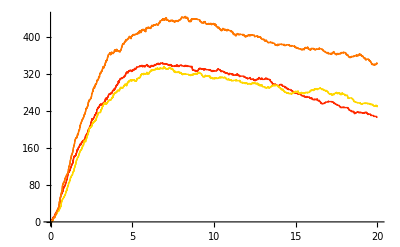

```mathematica
SSAPlot[ssim, {PX, PY, PZ}, PlotRange-> All]
```

```mathematica
xr=SSAtoXLR8R[r]
```

{{PZ↦X,hill[1,Km,-n,0,(α ϵ)/τ]},{PX↦Y,hill[1,Km,-n,0,(α ϵ)/τ]},{PY↦Z,hill[1,Km,-n,0,(α ϵ)/τ]},{X→∅,1/τ},{Y→∅,1/τ},{Z→∅,1/τ},{∅→X,(α0 ϵ)/τ},{∅→Y,(α0 ϵ)/τ},{∅→Z,(α0 ϵ)/τ},{X→PX+X,(Km β)/(ϵ τ)},{PX→∅,β/τ},{Y→PY+Y,(Km β)/(ϵ τ)},{PY→∅,β/τ},{Z→PZ+Z,(Km β)/(ϵ τ)},{PZ→∅,β/τ}}

```mathematica
xsim=run[xr, timeSpan-> 20, rates-> parameters, initialConditions-> iv];
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {PZ,Y,Z}

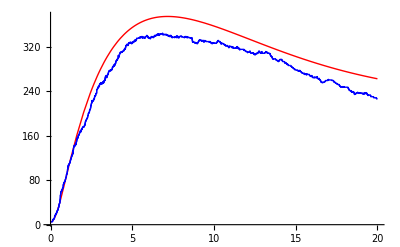

```mathematica
Show[runPlot[xsim, {PX}, holdLegend-> True],
SSAPlot[ssim, {PX}, SSAPlotStyles-> {Blue}], PlotRange-> All, Background-> White]
```